```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/scavgf/Library/CloudStorage/OneDrive-Personal/Spin-BosonModel

```mathematica
ListPlot[{ent0[[1;;All,{1,2}]],ent1[[1;;All,{1,2}]],ent2[[1;;All,{1,2}]],ent3[[1;;All,{1,2}]],ent42[[1;;All,{1,2}]]},PlotRange->{{0,20},{0,8}},Frame->True,PlotLegends->Automatic]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

-Graphics-

```mathematica
ent01=ENTASStx[80,"0.1",600,8000,"0.0025","0.0005"];
ent02=ENTASStx[80,"0.3",600,8000,"0.0025","0.0005"];
ent03=ENTASStx[80,"0.5",1200,16000,"0.00125","0.0005"];
ent04=ENTASStx[80,"0.7",1200,16000,"0.00125","0.0005"];
ent05=ENTASStx[80,"1.0",1200,16000,"0.00125","0.0005"];
ent06=ENTASStx[80,"1.2",2000,16000,"0.00125","0.0002"];
```

ASSMethod/data/entanglement-D-80-alpha-0.1-K=600-Nt=8000-Dt=0.0025-ep=0.0005.dat

ASSMethod/data/entanglement-D-80-alpha-0.3-K=600-Nt=8000-Dt=0.0025-ep=0.0005.dat

ASSMethod/data/entanglement-D-80-alpha-0.5-K=1200-Nt=16000-Dt=0.00125-ep=0.0005.dat

ASSMethod/data/entanglement-D-80-alpha-0.7-K=1200-Nt=16000-Dt=0.00125-ep=0.0005.dat

ASSMethod/data/entanglement-D-80-alpha-1.0-K=1200-Nt=16000-Dt=0.00125-ep=0.0005.dat

ASSMethod/data/entanglement-D-80-alpha-1.2-K=2000-Nt=16000-Dt=0.00125-ep=0.0002.dat

```mathematica
mean[list_,m_]:=Module[{L,list0,listx,m0},
L=Length@list;
m0=3;
list0=Table[Mean[list[[i;;If[i+m0>L,L,i+m0]]]],{i,1,18,m0}];
listx=Table[Mean[list[[i;;If[i+m>L,L,i+m]]]],{i,21,L,m}];
Join[list0,listx]
]
```

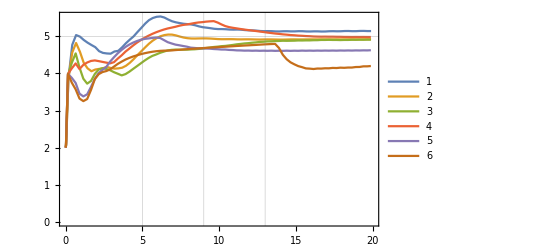

```mathematica
ListLinePlot[{mean[ent01[[1;;All,{1,2}]],100],mean[ent02[[1;;All,{1,2}]],100],mean[ent03[[1;;All,{1,2}]],200],mean[ent04[[1;;All,{1,2}]],200],mean[ent05[[1;;All,{1,2}]],200],mean[ent06[[1;;All,{1,2}]],200]},PlotRange->{{0,20},All},PlotRange->All,Frame->True,PlotLegends->Automatic,GridLines->{{5,9,13}}]
```

```mathematica
ent11=ENTHOtx[80,"0.1",600,2000,"0.01","0.0004"];
ent12=ENTHOtx[80,"0.3",600,2000,"0.01","0.0004"];
ent13=ENTHOtx[80,"0.5",600,2000,"0.01","0.0004"];
ent14=ENTHOtx[80,"0.7",600,2000,"0.01","0.0004"];
ent15=ENTHOtx[80,"1.0",600,2000,"0.01","0.0004"];
ent16=ENTHOtx[80,"1.2",600,2000,"0.01","0.0004"];
```

HOMethod/data/entanglement-D-80-alpha-0.1-K=600-Nt=2000-Dt=0.01-ep=0.0004-HO.dat

HOMethod/data/entanglement-D-80-alpha-0.3-K=600-Nt=2000-Dt=0.01-ep=0.0004-HO.dat

HOMethod/data/entanglement-D-80-alpha-0.5-K=600-Nt=2000-Dt=0.01-ep=0.0004-HO.dat

HOMethod/data/entanglement-D-80-alpha-0.7-K=600-Nt=2000-Dt=0.01-ep=0.0004-HO.dat

HOMethod/data/entanglement-D-80-alpha-1.0-K=600-Nt=2000-Dt=0.01-ep=0.0004-HO.dat

HOMethod/data/entanglement-D-80-alpha-1.2-K=600-Nt=2000-Dt=0.01-ep=0.0004-HO.dat

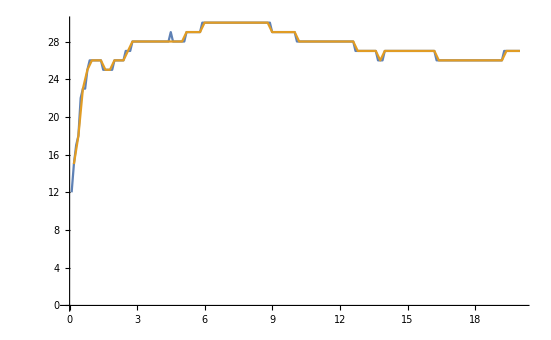

```mathematica
ListLinePlot[{ent12[[1;;All]],ent12[[2;;All;;2]]},PlotRange->All]
```

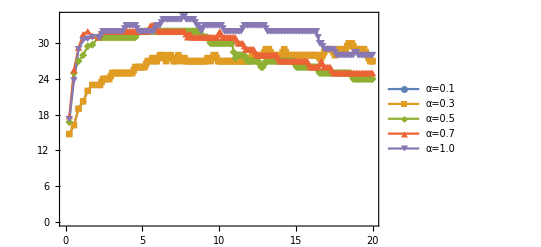

```mathematica
ListLinePlot[{mean[ent11,1],mean[ent11,1],mean[ent13,1],mean[ent14,1],mean[ent15,1]},PlotRange->{All,Automatic},Frame->True,PlotStyle->Thick,PlotLegends->LineLegend[{"α=0.1","α=0.3","α=0.5","α=0.7","α=1.0"}],PlotMarkers->Automatic]
```

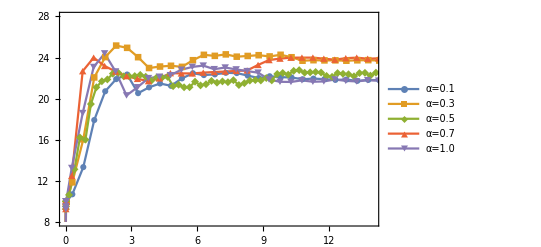

```mathematica
ListLinePlot[{mean[ent01[[All,{1,3}]],200],mean[ent02[[All,{1,3}]],200],mean[ent03[[All,{1,3}]],200],mean[ent04[[All,{1,3}]],400],mean[ent05[[All,{1,3}]],400]},PlotRange->{{0,14},{8,28}},Frame->True,PlotStyle->Thick,PlotLegends->LineLegend[{"α=0.1","α=0.3","α=0.5","α=0.7","α=1.0"}],PlotMarkers->Automatic]
```

```mathematica
szt0v=SZASStx[80,"0.1",600,8000,"0.0025","0.0005"];
szt1v=SZASStx[80,"0.3",600,8000,"0.0025","0.0005"];
szt2v=SZASStx[80,"0.5",1200,16000,"0.00125","0.0005"];
szt3v=SZASStx[80,"0.7",1200,16000,"0.00125","0.0005"];
szt4v=SZASStx[80,"1.0",1200,16000,"0.00125","0.0005"];
szt5v=SZASStx[80,"1.2",2000,16000,"0.00125","0.0002"];
```

ASSMethod/data/propagator-D-80-alpha-0.1-K=600-Nt=8000-Dt=0.0025-ep=0.0005.dat

ASSMethod/data/propagator-D-80-alpha-0.3-K=600-Nt=8000-Dt=0.0025-ep=0.0005.dat

ASSMethod/data/propagator-D-80-alpha-0.5-K=1200-Nt=16000-Dt=0.00125-ep=0.0005.dat

ASSMethod/data/propagator-D-80-alpha-0.7-K=1200-Nt=16000-Dt=0.00125-ep=0.0005.dat

ASSMethod/data/propagator-D-80-alpha-1.0-K=1200-Nt=16000-Dt=0.00125-ep=0.0005.dat

ASSMethod/data/propagator-D-80-alpha-1.2-K=2000-Nt=16000-Dt=0.00125-ep=0.0002.dat

ASSMethod/data/propagator-D-80-alpha-0.1-K=600-Nt=8000-Dt=0.0025-ep=0.0005.dat

ASSMethod/data/propagator-D-80-alpha-0.3-K=600-Nt=8000-Dt=0.0025-ep=0.0005.dat

ASSMethod/data/propagator-D-80-alpha-0.5-K=1200-Nt=16000-Dt=0.00125-ep=0.0005.dat

ASSMethod/data/propagator-D-80-alpha-0.7-K=1200-Nt=16000-Dt=0.00125-ep=0.0005.dat

ASSMethod/data/propagator-D-80-alpha-1.0-K=1200-Nt=16000-Dt=0.00125-ep=0.0005.dat

ASSMethod/data/propagator-D-80-alpha-1.2-K=2000-Nt=16000-Dt=0.00125-ep=0.0002.dat

```mathematica
szt0v1=SZHOtx[80,"0.1",600,2000,"0.01","0.0004"];
szt1v1=SZHOtx[80,"0.3",600,2000,"0.01","0.0004"];
szt2v1=SZHOtx[80,"0.5",600,2000,"0.01","0.0004"];
szt3v1=SZHOtx[80,"0.7",600,2000,"0.01","0.0004"];
szt4v1=SZHOtx[80,"1.0",600,2000,"0.01","0.0004"];
szt5v2=SZHOtx[80,"1.2",1200,4000,"0.005","0.0004"];
```

HOMethod/data/propagator-D-80-alpha-0.1-K=600-Nt=2000-Dt=0.01-ep=0.0004-HO.dat

HOMethod/data/propagator-D-80-alpha-0.3-K=600-Nt=2000-Dt=0.01-ep=0.0004-HO.dat

HOMethod/data/propagator-D-80-alpha-0.5-K=600-Nt=2000-Dt=0.01-ep=0.0004-HO.dat

HOMethod/data/propagator-D-80-alpha-0.7-K=600-Nt=2000-Dt=0.01-ep=0.0004-HO.dat

HOMethod/data/propagator-D-80-alpha-1.0-K=600-Nt=2000-Dt=0.01-ep=0.0004-HO.dat

HOMethod/data/propagator-D-80-alpha-1.2-K=1200-Nt=4000-Dt=0.005-ep=0.0004-HO.dat

```mathematica
szt5v1=SZHOtx[80,"1.2",1200,4000,"0.005","0.0002"];
```

HOMethod/data/propagator-D-80-alpha-1.2-K=1200-Nt=4000-Dt=0.005-ep=0.0002-HO.dat

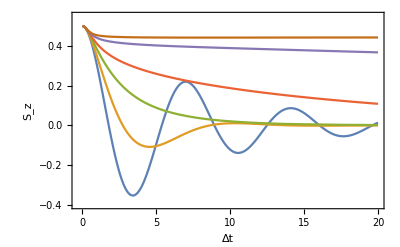

```mathematica
p10=ListLinePlot[{szt0v,szt1v,szt2v,szt3v,szt4v,szt5v},Frame->True,FrameLabel->{"Δt","S_z"},LabelStyle->Directive[20, FontFamily->"Times New Roman"],PlotRange->{{-0.3,20},{-0.4,0.55}}(*PlotLegends->LineLegend[{"α=0.1","α=0.3","α=0.5","α=0.7","α=1.0"}]*)]
```

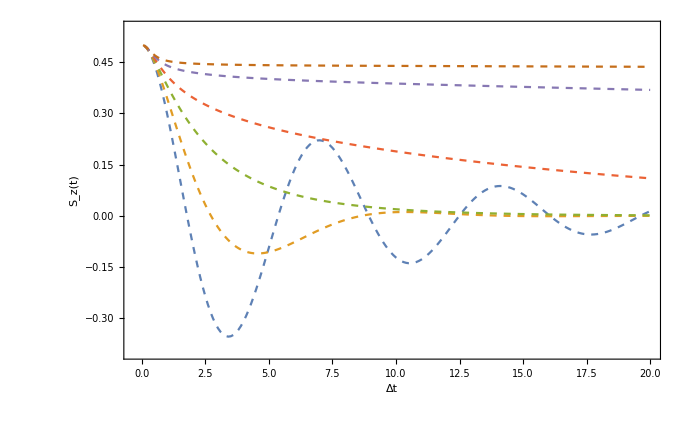

```mathematica
p1=ListLinePlot[{szt0v1,szt1v1,szt2v1,szt3v1,szt4v1,szt5v2},PlotStyle->Dashed,Frame->True,FrameLabel->{"Δt","S_z(t)"},LabelStyle->Directive[20, FontFamily->"Times New Roman"],PlotRange->{{-0.3,20},{-0.4,0.55}}(*PlotLegends->LineLegend[{"α=0.1","α=0.3","α=0.5","α=0.7","α=1.0"}]*)]
```

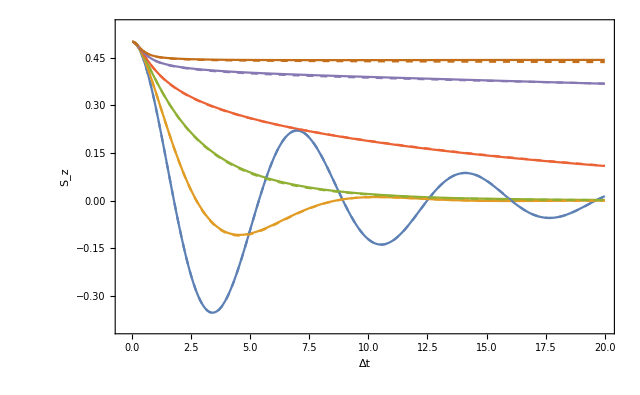

```mathematica
Show[p10,p1]
```

```mathematica
p2=ListPlot[{szt0v1[[1;;All;;20]],szt1v1[[1;;All;;20]],szt2v1[[1;;All;;20]],szt3v1[[1;;All;;20]],szt4v1[[1;;All;;20]],szt5v2[[1;;All;;20]]},Frame->True,FrameLabel->{"Δt","S_z"},LabelStyle->Directive[20, FontFamily->"Times New Roman"],PlotRange->{{0,20},{-0.4,0.55}},(*PlotLegends->LineLegend[{"α=0.1","α=0.3","α=0.5","α=0.7","α=1.0"}],*)PlotMarkers->Automatic];
```

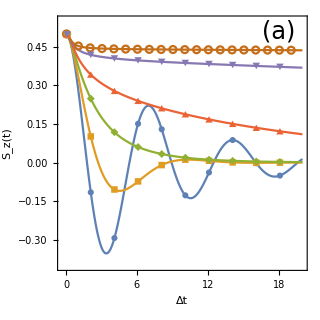

```mathematica
P1=Show[{p1,p2},AspectRatio->1,ImageSize->320,Epilog->Inset[Style["(a)",{24,FontFamily->"Times New Roman"}],{18,0.51}],PlotRangeClipping->False]
```

```mathematica
(*P2=ListLinePlot[{mean[ent01[[All,{1,3}]],200],mean[ent02[[All,{1,3}]],200],mean[ent03[[All,{1,3}]],200],mean[ent04[[All,{1,3}]],400],mean[ent05[[All,{1,3}]],400],mean[ent05[[All,{1,3}]],400]},PlotRange->{{-0.3,20},{8,26.5}},Frame->True,PlotStyle->Thick,PlotLegends->Placed[LineLegend[{"α=0.1","α=0.3","α=0.5","α=0.7","α=1.0","α=1.2"},LabelStyle->Directive[16]],{0.8,0.4}],LabelStyle->Directive[20,Black, FontFamily->"Times New Roman"],PlotMarkers->Automatic,FrameLabel->{"Ωt","D_max"},FrameLabel->{"Ωt","S_z"},ImageSize->300,AspectRatio->1,Epilog->Inset[Style["(b)",{24,FontFamily->"Times New Roman"}],{18.5,25.3}],PlotRangeClipping->False]*)
```

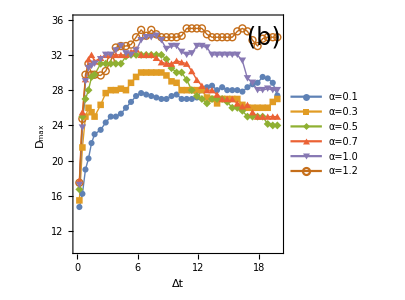

```mathematica
P2=ListLinePlot[{mean[ent11,5],mean[ent12,5],mean[ent13,5],mean[ent14,5],mean[ent15,5
],mean[ent16,5]},PlotRange->{{0.0,20.0},{10,36}},Frame->True,PlotStyle->Thick,PlotLegends->Placed[LineLegend[{"α=0.1","α=0.3","α=0.5","α=0.7","α=1.0","α=1.2"},LabelStyle->Directive[15,Background->Opacity[0.3,White]]],{0.82,0.34}],LabelStyle->Directive[20,Black, FontFamily->"Times New Roman"],PlotMarkers->Automatic,FrameLabel->{"Δt","D_max"},FrameLabel->{"Δt","S_z"},ImageSize->300,AspectRatio->1,Epilog->Inset[Style["(b)",{24,FontFamily->"Times New Roman"},Background->White],{18.5,34}],PlotRangeClipping->False]
```

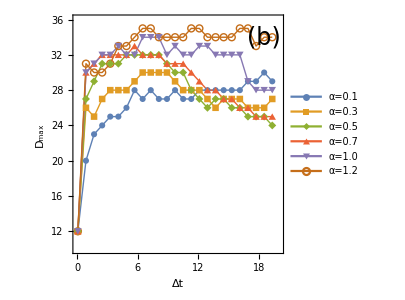

```mathematica
m1=8;
P2=ListLinePlot[{ent11[[1;;All;;m1]],ent12[[1;;All;;m1]],ent13[[1;;All;;m1]],ent14[[1;;All;;m1]],ent15[[1;;All;;m1]],ent16[[1;;All;;m1]]},PlotRange->{{0.0,20.0},{10,36}},Frame->True,PlotStyle->Thick,PlotLegends->Placed[LineLegend[{"α=0.1","α=0.3","α=0.5","α=0.7","α=1.0","α=1.2"},LabelStyle->Directive[15,Background->Opacity[0.3,White]]],{0.82,0.34}],LabelStyle->Directive[20,Black, FontFamily->"Times New Roman"],PlotMarkers->Automatic,FrameLabel->{"Δt","D_max"},FrameLabel->{"Δt","S_z"},ImageSize->300,AspectRatio->1,Epilog->Inset[Style["(b)",{24,FontFamily->"Times New Roman"},Background->White],{18.5,34}],PlotRangeClipping->False]
```

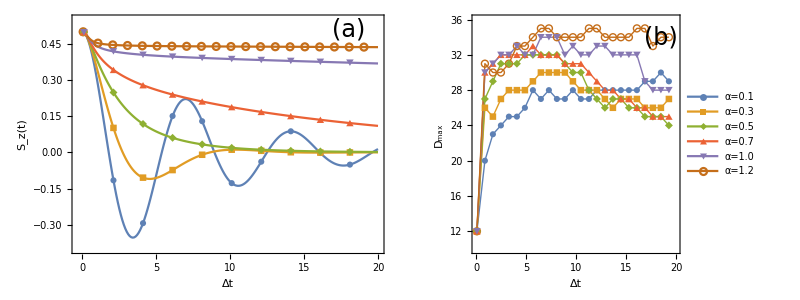

```mathematica
P3=Grid[{{P1,P2}}]
```

```mathematica
Export["SBM.pdf",P3]
```

SBM.pdf

```mathematica
m=20;
```

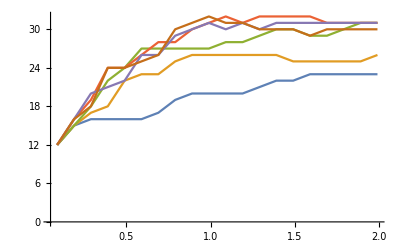

```mathematica
ListLinePlot[{ent11[[1;;m]],ent12[[1;;m]],ent13[[1;;m]],ent14[[1;;m]],ent15[[1;;m]],ent16[[1;;m]]},PlotRange->All]
```

```mathematica
ent31=ENTHOtx[80,"0.5",100,100,"0.01","0.0004"];
ent32=ENTHOtx[80,"0.5",200,200,"0.005","0.0004"];
ent33=ENTHOtx[80,"0.5",400,400,"0.0025","0.0004"];
ent34=ENTHOtx[80,"0.5",800,800,"0.00125","0.0004"];
```

HOMethod/data/entanglement-D-80-alpha-0.5-K=100-Nt=100-Dt=0.01-ep=0.0004-HO.dat

HOMethod/data/entanglement-D-80-alpha-0.5-K=200-Nt=200-Dt=0.005-ep=0.0004-HO.dat

HOMethod/data/entanglement-D-80-alpha-0.5-K=400-Nt=400-Dt=0.0025-ep=0.0004-HO.dat

HOMethod/data/entanglement-D-80-alpha-0.5-K=800-Nt=800-Dt=0.00125-ep=0.0004-HO.dat

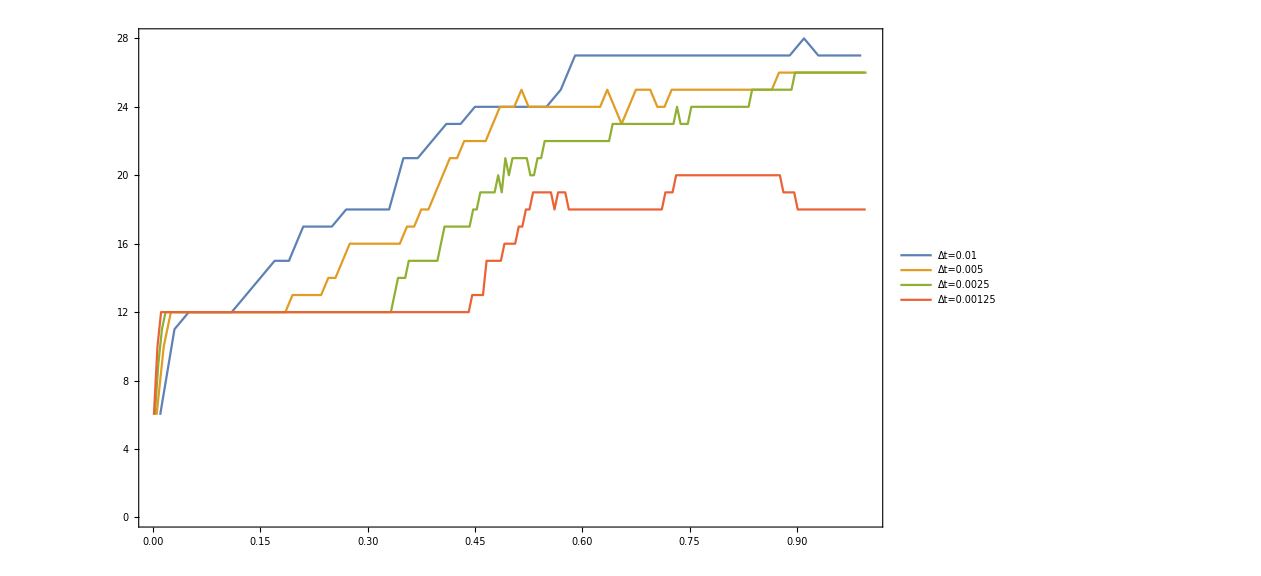

```mathematica
ListPlot[{ent31[[1;;All;;2,All]],ent32[[1;;All;;2]],ent33[[1;;All;;2]],ent34[[1;;All;;4]]},Joined->True,PlotRange->{{0,1},Automatic},Frame->True,PlotLegends->{"Δt=0.01","Δt=0.005","Δt=0.0025","Δt=0.00125"}]
```

```mathematica
szt31=SZHOtx[80,"0.5",100,100,"0.01","0.0004"];
szt32=SZHOtx[80,"0.5",200,200,"0.005","0.0004"];
szt33=SZHOtx[80,"0.5",400,400,"0.0025","0.0004"];
szt34=SZHOtx[80,"0.5",800,800,"0.00125","0.0004"];
```

HOMethod/data/propagator-D-80-alpha-0.5-K=100-Nt=100-Dt=0.01-ep=0.0004-HO.dat

HOMethod/data/propagator-D-80-alpha-0.5-K=200-Nt=200-Dt=0.005-ep=0.0004-HO.dat

HOMethod/data/propagator-D-80-alpha-0.5-K=400-Nt=400-Dt=0.0025-ep=0.0004-HO.dat

HOMethod/data/propagator-D-80-alpha-0.5-K=800-Nt=800-Dt=0.00125-ep=0.0004-HO.dat

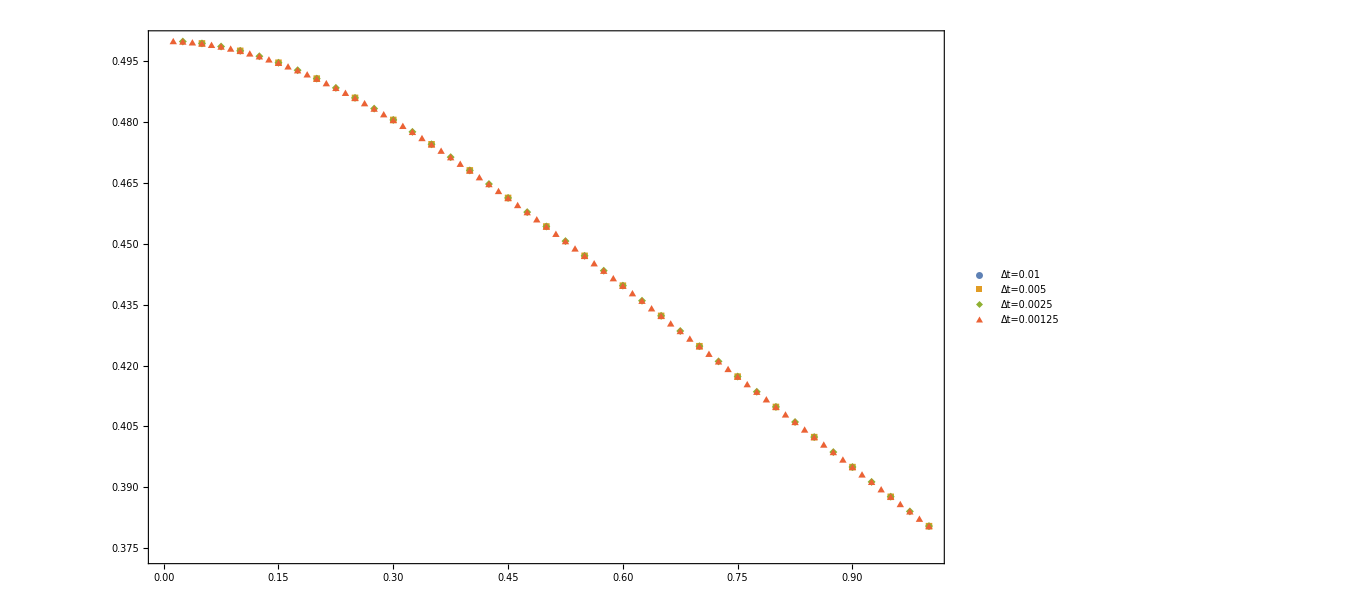

```mathematica
ListPlot[{szt31,szt32,szt33,szt34},PlotRange->{{0,1},Automatic},Frame->True,PlotLegends->{"Δt=0.01","Δt=0.005","Δt=0.0025","Δt=0.00125"},PlotMarkers->Automatic]
```

```mathematica
a=ConstantArray[1,{3}]
```

{1,1,1}

```mathematica
A=2*KroneckerProduct[ArrayReshape[KroneckerProduct[a,a],{9}],ConstantArray[1,{3}]/2]
```

{{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1}}

```mathematica
{u,d,v}=SingularValueDecomposition[N[A]]
```

{{{-0.333333,0.942809,2.08316×10^-16,9.25186×10^-18,-9.25186×10^-18,9.25186×10^-18,0.,-3.70074×10^-17,-3.70074×10^-17},{-0.333333,-0.117851,0.935414,-8.37458×10^-18,-1.30005×10^-17,1.04097×10^-17,2.68811×10^-17,3.17175×10^-17,4.55953×10^-17},{-0.333333,-0.117851,-0.133631,-0.377964,-0.377964,-0.377964,-0.377964,-0.377964,-0.377964},{-0.333333,-0.117851,-0.133631,0.896327,-0.103673,-0.103673,-0.103673,-0.103673,-0.103673},{-0.333333,-0.117851,-0.133631,-0.103673,0.896327,-0.103673,-0.103673,-0.103673,-0.103673},{-0.333333,-0.117851,-0.133631,-0.103673,-0.103673,0.896327,-0.103673,-0.103673,-0.103673},{-0.333333,-0.117851,-0.133631,-0.103673,-0.103673,-0.103673,0.896327,-0.103673,-0.103673},{-0.333333,-0.117851,-0.133631,-0.103673,-0.103673,-0.103673,-0.103673,0.896327,-0.103673},{-0.333333,-0.117851,-0.133631,-0.103673,-0.103673,-0.103673,-0.103673,-0.103673,0.896327}},{{5.19615,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}},{{-0.57735,0.816497,5.60772×10^-17},{-0.57735,-0.408248,-0.707107},{-0.57735,-0.408248,0.707107}}}

```mathematica
u[[;;,1]]
```

{-0.333333,-0.333333,-0.333333,-0.333333,-0.333333,-0.333333,-0.333333,-0.333333,-0.333333}

```mathematica
v†//MatrixForm
```

```mathematica
({{d, □, □}, {0.8164965809277259, -0.408248290463863, -0.40824829046386313}, {5.607715848155152*^-17, -0.7071067811865476, 0.7071067811865475}})
```

```mathematica
√9.0*√3
```

5.19615